This Mathematica notebook requires the CRNSimulator package.  It can be downloaded from: http://dna.caltech.edu/SupplementaryMaterial/DNA_for_CRNs/

We try to load it from the same directory as this notebook:

```mathematica
nbdir=DirectoryName[ToFileName["FileName"/.NotebookInformation[SelectedNotebook[]]]];
```

```mathematica
Get["CRNSimulator.m",Path->nbdir]
```

## Code

### Code to convert formal CRN to DNA implementation

Code assumes cmax and qmax globals.

Produces reactions in srxn[[reaction index],{x1,x2},{x3},k] format ("structured reaction system"):

```mathematica
rxnsysToSrxnsys[rsys_]:=
Module[{i=1},
rsys/.
rxn[rs_,ps_,k_]:>
srxn[i++,
{Unevaluated[rs]/.{Plus->Seq,c_Integer*s_:>Seq@@Table[s,{c}] }},{Unevaluated[ps]/.{Plus->Seq,c_Integer*s_:>Seq@@Table[s,{c}] }},
k]]
```

Totals formal rate constants of bimolecular reactions with s as the first reactant:

```mathematica
computeSigmaj[s_,rsys_]:=Total[Cases[rxnsysToSrxnsys[rsys],srxn[_,{s,_},_,k_]:>k]]
```

Maximum over s:

```mathematica
computeSigma[rsys_]:=Max[computeSigmaj[#,rsys]&/@SpeciesInRxnsys[rsys]]
```

Compute γ as discussed in the text:

```mathematica
computeGamma[rsys_]:=qmax^-1(qmax-computeSigma[rsys])
```

Find the lower-bound on qmax as discussed in the text. Note that the generateBufferingModules → False option can be used when buffering modules are not wanted.

```mathematica
Options[computeQmaxLowerBound]={generateBufferingModules->True};
```

```mathematica
computeQmaxLowerBound[rsys_,OptionsPattern[]]:=
Module[{σ=computeSigma[rsys],srsys=rxnsysToSrxnsys[rsys]},
Max[
Cases[srsys,srxn[_,{_},_,k_]:>k/cmax+σ],
Cases[srsys,srxn[_,{_,_},_,k_]:>k+σ],
If[OptionValue[generateBufferingModules],
(2σ-computeSigmaj[#,rsys])&  /@  SpeciesInRxnsys[rsys],
0]
]]
```

Definitions of reaction and buffering modules:

Bimolecular reaction module:

```mathematica
dnarxn[i_,{r1_,r2_},{ps__},k_,γ_]:=
Seq[
revrxn[r1+gateL[i],gateH[i]+strandB[i],γ^-1 k ,qmax],
rxn[r2+gateH[i],strandO[i],qmax],
rxn[strandO[i]+gateT[i],Plus[ps],qmax],

conc[{gateL[i],strandB[i],gateT[i]},cmax]
]
```

Unimolecular reaction module:

```mathematica
dnarxn[i_,{r1_},{ps___},k_,γ_]:=
Seq[
rxn[r1+gateG[i],strandO[i],γ^-1 k /cmax],
rxn[strandO[i]+gateT[i],Plus[ps],qmax],

conc[{gateG[i],gateT[i]},cmax]
]
```

Buffering reaction module:

```mathematica
dnabalrxn[s_,γ_,σ_,σj_]:=
Module[{j=ToString[s]},
Seq[
revrxn[s+gateLS[j],gateHS[j]+strandBS[j],γ^-1(σ-σj),qmax],

conc[{gateLS[j],strandBS[j]},cmax]
]]
```

Main function to convert a formal CRN to the DNA implementation.  Note that the generateBufferingModules → False option can be used when buffering modules are not wanted.

```mathematica
Options[rxnsysToDnasys]={generateBufferingModules->True};
```

```mathematica
rxnsysToDnasys[rsys_,OptionsPattern[]]:=
Module[
{γ=computeGamma[rsys],
σ=computeSigma[rsys]},
Join[
rxnsysToSrxnsys[rsys]/.
{srxn[i_,rs_,ps_,k_]:>dnarxn[i,rs,ps,k,γ],
conc[s_,c_]:>conc[s,γ^-1 c]},
If[computeSigmaj[#,rsys]<σ && OptionValue[generateBufferingModules],
dnabalrxn[#,γ,σ,computeSigmaj[#,rsys]],Seq[]]&  
/@  SpeciesInRxnsys[rsys]]
]
```

Computes the concentration and time scaling factors for the DNA system so that largest concentration cmax is maxconc (usually 10^-5), and max rate constant qmax is maxrateconst (usually 10^6):

```mathematica
computeConcAndTimeScaling[maxconc_,maxrateconst_]:=
{maxconc/cmax, (maxconc/cmax)^-1(maxrateconst/qmax)^-1}
```

### Code for controlling simulations

Given a solution, generates a new reaction system with the initial concentrations given by the final concentrations of the solution.

```mathematica
rsysForRestart[rsys_,sol_,tmax_]:=
Join[
rsys/.conc[___]->Seq[],
conc[#,(#[tmax]/.sol)]&/@SpeciesInRxnsys[rsys]]
```

For formal functions of one argument, whose definitions are valid starting at 0 ending at end1 and end2.  Make new function which uses the second one when first one ends:

```mathematica
joinFunctions[f1_,f2_,end1_,end2_]:=
Function[Evaluate[Which@@{0≤#<end1, f1[#],end1≤#<end1+end2, f2[#-end1]}]]
```

Main function for simulating a reaction system using a schedule of addition/removal of species, rather than just starting in one initial configuration.  (In rxnsys, x1 must not have initial conc):

```mathematica
simulateRxnsysWithSchedule[rxnsys_,schedule_,x1_]:=
simulateRxnsysWithSchedule[rxnsys,schedule,{x1}]
```

```mathematica
simulateRxnsysWithSchedule::undershoot="Scheduled decrease (schedule step `1`: `2`) resulted in negative concentration. Going to 0.";
```

```mathematica
simulateRxnsysWithSchedule[rxnsys_,schedule_,xs_List]:=
Module[
{n=Length[schedule],rsys,lastsol,sol},

rsys=Join[rxnsys, MapIndexed[conc[#1,schedule⟦1,1+#2⟦1⟧⟧]&,xs]];
lastsol=SimulateRxnsys[rsys,schedule⟦1,1⟧];
sol=lastsol;

Do[
rsys=
rsysForRestart[rsys,lastsol,schedule⟦i-1,1⟧]/.
MapIndexed[
conc[#1,s_]:>
(If[s+schedule⟦i,1+#2⟦1⟧⟧<0,
Message[simulateRxnsysWithSchedule::undershoot,i,schedule⟦i,1+#2⟦1⟧⟧]];
conc[#1,Max[0,s+schedule⟦i,1+#2⟦1⟧⟧]])&,
xs];
lastsol=SimulateRxnsys[rsys,schedule⟦i,1⟧];
sol=MapThread[#1/.(s_->f1_):>(s->joinFunctions[f1,#2/.(_->f2_):>f2,Total[schedule⟦;;i-1,1⟧],Total[schedule⟦;;i,1⟧]])&,
{sol,lastsol}],

{i,2,n}];

sol
]
```

Since some species are buffered, we may not be able to instantaneously decrease concentration because this may result in going negative.  We do 1/3 of the distance, then 1/3 of the remaining distance, etc (here 3 is the stepfactor).  Rescaled so that after all iterations we cover the whole distance.

```mathematica
steppizeSchedule[schedule_,iterations_,stepfactor_:3,stepduration_:0.01]:=
Module[{sum=1-((stepfactor-1)/(stepfactor))^(iterations)},
Map[
Seq@@Table[Prepend[N[Rest[#]]* (stepfactor-1)^(i-1)(stepfactor)^(-i) / sum,If[i==iterations,First[#],stepduration]],{i,1,iterations}]&,
schedule]]
```

### Code for modifying reaction system

Adds waste product w[i] to reaction i.  This is useful for monitoring the total flow through reactions.

```mathematica
addWasteProducts[rsys_,w_]:=
Module[{i=1},
rsys/.  
rxn[rs_,ps_,k_]:>
With[{pse=Replace[Plus[ps,w[i++]],1->0,1]},rxn[rs,pse,k]]
]
```

## DNA Tag Stability in Solution - Simulation

#### Stability of DNA Bit 1 and Bit 0 in solution of 10mM MgCl2.

```mathematica
(* 
x1 = Bit1, x2 = Bit0, x3 = blocker, x4 = blocked Bit1, x5 = dissocated Bit0; 
Conc unit: µM;
Initial concentrations of Bit 1 and Bit 0 = 4 µM;
Blocker strand = 'CTCTCCTTATCAAACCACCAC';
dG of Blocker strand = -13.99 kcal/mol;
Hybridization rate constant (k_hyb) = 1e6 M^-1•s^-1 = 1 µM^-1•s^-1;
Dissociation rate constant = k_hyb/(exp(-dG/(T*R))) = 5.45e-5 M^-1•s^-1 = 5.45e-11 M^-1•s^-1;
Time step = 1 second. 
*)


rsys={
rxn[x1+x3,x4,1], (*Bit1 + blocker hybridization *)
(* reactant, product, rate constant*)
rxn[x2,x5 + x3,0.0000000000545],(* Bit 0 dissociation*)
rxn[x4, x1+x3, 0.0000000000545],
rxn[x3+x5, x2,1],

conc[x1,4], (* initial concentration, µM*)
conc[x2,4],
conc[x3,0],
conc[x4,0],
conc[x5,0]

};
```

```mathematica
tmax=3600*24*365*2000;
```

```mathematica
sol=SimulateRxnsys[rsys,tmax];
```

```mathematica
plotter=
#[t]/.sol&/@{x1,x2,x4,x5};
```

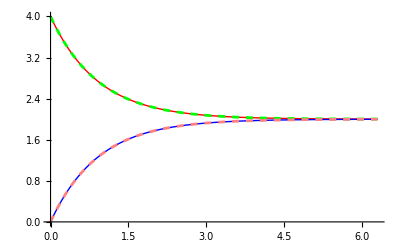

```mathematica
Plot[plotter,{t,0,tmax},PlotPoints->300,PlotRange->{0,All},PlotStyle->{{Red,Thick},{Green,Dashed},{Blue,Thick},{Pink,Dashed}}]
```